Null^2

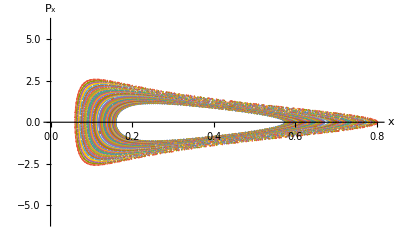

```mathematica
ClearAll["Global`*"]; 
(*Parametros iniciales*)
E0 =-1.7;
PyInicial = 1.0;
ϵ0 = 0.0;
w0=(3/4);
Windingpos[W_]:= ((-0.5)*((1/(1-W))^(2/3)))-E0;
(*Definicion Hmailtoneano*)
H[px_,py_,x_,y_,ϵ_] := (1/2)(px^2 +py^2)+(px*y-py*x)-((1-ϵ)/((x+ϵ)^2 + y^2)^(1/2))-(ϵ/((x+ϵ-1)^2 + y^2)^(1/2))
(*ecuaciones de Hamilton*)
D[H[px,py,x,y,ϵ],px];
xpunto = D[H[px,py,x,y,ϵ],px]/.{px->px[t],y->y[t],x->x[t],py->py[t]};
ypunto = D[H[px,py,x,y,ϵ],py]/.{px->px[t],y->y[t],x->x[t],py->py[t]};
pxpunto = -D[H[px,py,x,y,ϵ],x]/.{px->px[t],y->y[t],x->x[t],py->py[t]};
pypunto =  -D[H[px,py,x,y,ϵ],y]/.{px->px[t],y->y[t],x->x[t],py->py[t]};
(*Solución ecuaciones diferenciales en terminos de las condiciones iniciales *)
psect[{pox_,poy_,x0_,y0_,ϵ0_}]:=Reap[NDSolve[{x'[t]== xpunto /.{ϵ->ϵ0},y'[t]==ypunto/.{ϵ->ϵ0},px'[t]==pxpunto/.{ϵ->ϵ0}, py'[t]==pypunto /.{ϵ->ϵ0},x[0]==x0,y[0]==y0,px[0]==pox,py[0]==poy,WhenEvent[{y[t]==0 && y'[t]<0},Sow[{x[t],px[t]}]]},{},{t,1,500},MaxSteps->∞]][[-1,1]]
(*Gráfica*)
(*Condiciones iniciales que conserven energia, momento en x en función de la energia y x*)
Px[x_]:= Solve[H[px,PyInicial,x,0,ϵ0] == E0,px,Reals]
(*Tabla de condiciones iniciales para x desde 0.2 hasta 0.3 en pasos de 0.01*)
ConIni= Table[{Abs[px /.Px[i][[1]]],PyInicial,0,i,ϵ0},{i,Windingpos[w0]-0.1,Windingpos[w0]+0.1,0.005}];
(*Soluciones de las ecuaciones diferenciales en función de todas las condiciones iniciales*)
Datos =Map[psect, ConIni];
(*Gráfica*)
ListPlot[Datos,PlotRange->{{Automatic,Automatic},{-6,6}},AxesLabel->{"x",HoldForm[Subscript[P,x]]}](*,PlotLabel->"Poincare section for P_y0=0, ϵ="<>ToString[ϵ0]]
*)
```

```mathematica
ClearAll["Global`*"];
```